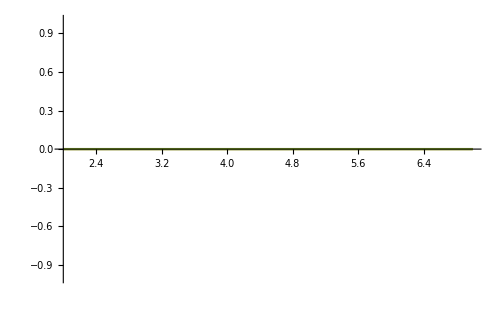

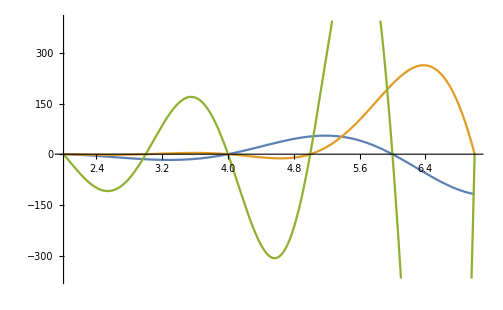

```mathematica
Plot[{LegendreP[x,3,Cos[0]],LegendreP[x,6,Cos[0]],LegendreP[x,9,Cos[0]]},{x,2,7}]
Plot[{LegendreP[x,3,Cos[π/2]],LegendreP[x,6,Cos[π/2]]/50,LegendreP[x,9,Cos[π/2]]/200},{x,2,7}]
```

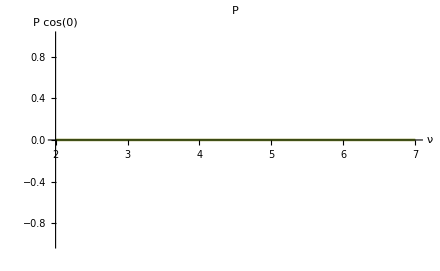

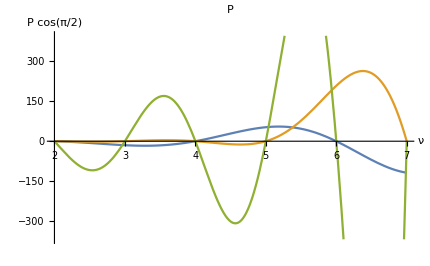

```mathematica
Show[%74,AxesLabel->{HoldForm[ν],HoldForm[P Cos[0]]},PlotLabel->HoldForm[P],LabelStyle->{GrayLevel[0]}]
Show[%75,AxesLabel->{HoldForm[ν],HoldForm[P Cos[π/2]]},PlotLabel->HoldForm[P],LabelStyle->{GrayLevel[0]}]
```

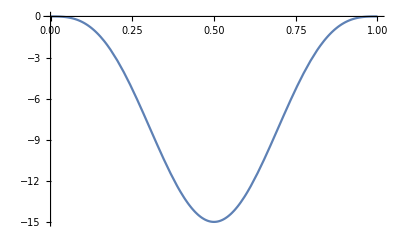

```mathematica
Plot[LegendreP[3,3,Cos[π*x]],{x,0,1}]
```

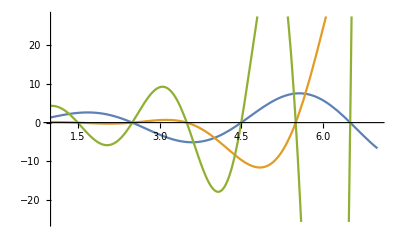

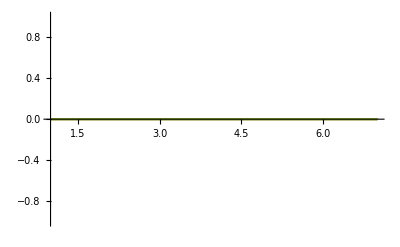

```mathematica
Plot[{LegendreQ[x,3/2,Cos[π/2]],LegendreQ[x,9/2,Cos[π/2]]/50,LegendreQ[x,15/2,Cos[π/2]]/250},{x,1,7}]
Plot[{LegendreQ[x,3/2,Cos[0]],LegendreQ[x,9/2,Cos[0]],LegendreQ[x,9/2,Cos[0]]},{x,1,7}]
```

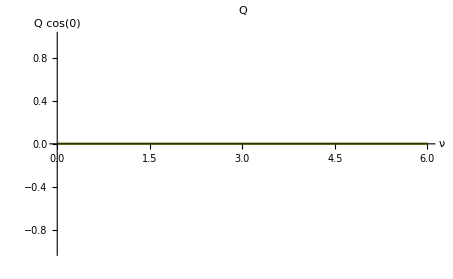

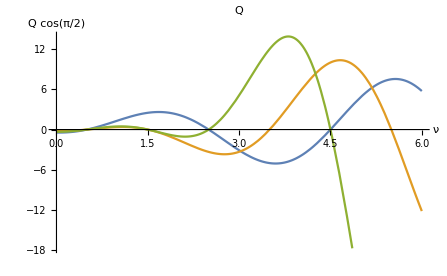

```mathematica
Show[%27,AxesLabel->{HoldForm[ν],HoldForm[Q (Cos[0])]},PlotLabel->HoldForm[Q],LabelStyle->{GrayLevel[0]}]
Show[%26,AxesLabel->{HoldForm[ν],HoldForm[Q( Cos[π/2])]},PlotLabel->HoldForm[Q],LabelStyle->{GrayLevel[0]}]
```

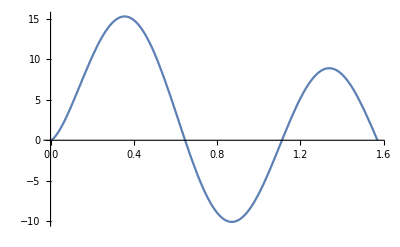

```mathematica
Plot[LegendreQ[13/2,3/2,Cos[x]],{x,0,π/2}]
```

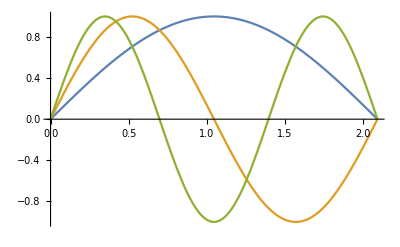

(1-Cos[n π^2])/(n π)

-(2 (-1+Cos[m π]))/(3 m)

```mathematica
Plot[{Sin[3/2*x],Sin[3*x],Sin[9/2*x]},{x,0,2/3*π}]
Integrate[Sin[n*π*x],{x,0,π}]
Integrate[Sin[m*3/2*x],{x,0,2/3*π}]
```

```mathematica
-(2 (-1+Cos[m π]))/(3 m)
```

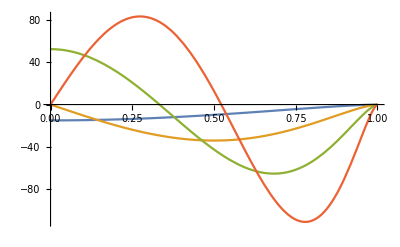

21

9/2

363/8

```mathematica
Plot[{LegendreP[3,3,z],LegendreP[4,3,z],LegendreP[5,3,z],LegendreP[6,3,z]},{z,0,1}]
Integrate[LegendreP[4,3,z],{z,1,0}]
Integrate[LegendreP[6,3,z],{z,1,0}]
Integrate[LegendreP[8,3,z],{z,1,0}]
```

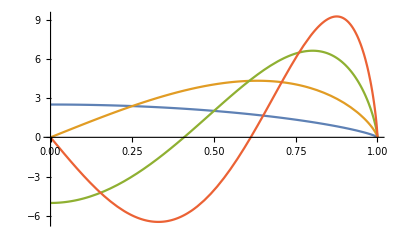

∫_1^0 LegendreQ[3/2,3/2,z]ⅆz

∫_1^0 LegendreQ[5/2,3/2,z]ⅆz

∫_1^0 LegendreQ[7/2,3/2,z]ⅆz

```mathematica
Plot[{LegendreQ[3/2,3/2,z],LegendreQ[5/2,3/2,z],LegendreQ[7/2,3/2,z],LegendreQ[9/2,3/2,z]},{z,0,1}]
Integrate[LegendreQ[3/2,3/2,z],{z,1,0}]
Integrate[LegendreQ[5/2,3/2,z],{z,1,0}]
Integrate[LegendreQ[7/2,3/2,z],{z,1,0}]
```

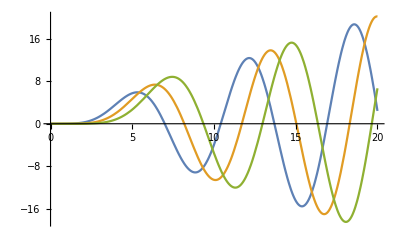

(8 ζ+7 ζ Cos[ζ]+(-15+ζ^2) Sin[ζ])/ζ^4

(ζ (105-2 ζ^2) Cos[ζ]+(-105+22 ζ^2) Sin[ζ]+15 ζ^2 SinIntegral[ζ])/(2 ζ^5)

(16 ζ^3+(315 ζ-16 ζ^3) Cos[ζ]-(315-105 ζ^2+ζ^4) Sin[ζ])/ζ^6

(ζ (20790-1575 ζ^2+8 ζ^4) Cos[ζ]+(-20790+8505 ζ^2-176 ζ^4) Sin[ζ]+105 ζ^4 SinIntegral[ζ])/(8 ζ^7)

```mathematica
Plot[{r^2*SphericalBesselJ[3,r],r^2*SphericalBesselJ[4,r],r^2*SphericalBesselJ[5,r]},{r,0,20}]
Integrate[r^2*SphericalBesselJ[3,ζ*r],{r,0,1}]
Integrate[r^2*SphericalBesselJ[4,ζ*r],{r,0,1}]
Integrate[r^2*SphericalBesselJ[5,ζ*r],{r,0,1}]
Integrate[r^2*SphericalBesselJ[6,ζ*r],{r,0,1}]
```

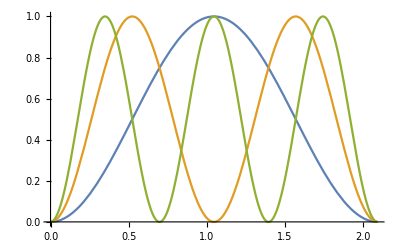

π/3-Sin[2 m π]/(6 m)

```mathematica
Plot[{Sin[3/2*x]^2,Sin[3*x]^2,Sin[9/2*x]^2},{x,0,2/3*π}]
Integrate[Sin[m*3/2*x]^2,{x,0,2/3*π}]
```

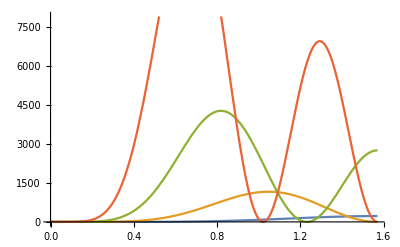

```mathematica
Plot[{LegendreP[3,3,Cos[θ]]^2,LegendreP[4,3,Cos[θ]]^2,LegendreP[5,3,Cos[θ]]^2,LegendreP[6,3,Cos[θ]]^2},{θ,0,π/2}]
Integrate[LegendreP[4,3,Cos[θ]]^2,{θ,0,π/2}];
Integrate[LegendreP[6,3,z]^2,{z,1,0}];
Integrate[LegendreP[8,3,z]^2,{z,1,0}];
```

```mathematica
ν=8;
μ=3;
-((ν+μ)!)/((2*ν+1)*(ν-μ)!)
Integrate[LegendreP[ν,μ,z]^2,{z,1,0}]
NIntegrate[LegendreP[ν,μ,z]^2,{z,1,0}]
```

-332640/17

-332640/17

-19567.1

```mathematica
Clear[ν,μ]
((ν+μ)!)/((2*ν+1)*(ν-μ)!)
Integrate[LegendreQ[ν,μ,z]^2,{z,1,0}]
NIntegrate[LegendreQ[ν,μ,z]^2,{z,1,0}]
```

((μ+ν)!)/((1+2 ν) (-μ+ν)!)

∫_1^0 LegendreQ[ν,μ,z]^2 ⅆz

NIntegrate::inumr: The integrand LegendreQ[ν,μ,z]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{1,0}}.

NIntegrate[LegendreQ[ν,μ,z]^2,{z,1,0}]

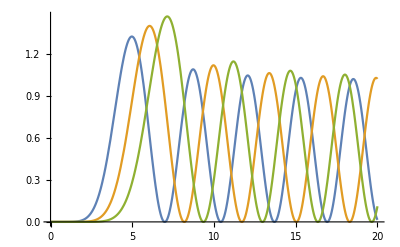

1/(2 ζ31^8)(-45-15 ζ31^2-6 ζ31^4+ζ31^6+(45-75 ζ31^2+6 ζ31^4) Cos[2 ζ31]+ζ31 (180-60 ζ31^2+ζ31^4) Cos[ζ31] Sin[ζ31])

-1/(4 ζ^10)(3150+630 ζ^2+90 ζ^4+20 ζ^6-2 ζ^8+10 (-315+567 ζ^2-93 ζ^4+2 ζ^6) Cos[2 ζ]+ζ (-6300+2940 ζ^2-180 ζ^4+ζ^6) Sin[2 ζ])

1/(4 ζ^12)(-198450+2 ζ^2 (-14175-1260 ζ^2-105 ζ^4-15 ζ^6+ζ^8)+30 (6615-12285 ζ^2+2604 ζ^4-119 ζ^6+ζ^8) Cos[2 ζ]+ζ (396900-207900 ζ^2+20160 ζ^4-420 ζ^6+ζ^8) Sin[2 ζ])

-1/(4 ζ^14)(19646550+2182950 ζ^2+141750 ζ^4+7560 ζ^6+420 ζ^8+42 ζ^10-2 ζ^12+42 (-467775+883575 ζ^2-211275 ζ^4+13500 ζ^6-250 ζ^8+ζ^10) Cos[2 ζ]+ζ (-39293100+21829500 ζ^2-2611980 ζ^4+90720 ζ^6-840 ζ^8+ζ^10) Sin[2 ζ])

```mathematica
Plot[{r^2*SphericalBesselJ[3,r]^2,r^2*SphericalBesselJ[4,r]^2,r^2*SphericalBesselJ[5,r]^2},{r,0,20}]
Integrate[r^2*SphericalBesselJ[3,ζ31*r]^2,{r,0,1}]
Integrate[r^2*SphericalBesselJ[4,ζ*r]^2,{r,0,1}]
Integrate[r^2*SphericalBesselJ[5,ζ*r]^2,{r,0,1}]
Integrate[r^2*SphericalBesselJ[6,ζ*r]^2,{r,0,1}]
```

```mathematica
Q DEL:
```

```mathematica
Integrate[LegendreP[n,m,z]^2,{z,1,0}]
Integrate[LegendreQ[n,m,z]^2,{z,1,0}]
```

∫_1^0 LegendreP[n,m,z]^2 ⅆz

∫_1^0 LegendreQ[n,m,z]^2 ⅆz

```mathematica
GRADIENT
```

```mathematica
Grad[f,{Subscript[x, 1],…,Subscript[x, n]}]
```

```mathematica
Integrate[ϕ*Sin[3/2m *ϕ],{ϕ,0,2π/3}]
```

-(4 (m π Cos[m π]-Sin[m π]))/(9 m^2)

```mathematica
ζ[a_,b_]:=N[BesselJZero[a+1/2,b]];
```

```mathematica
B[ν_,μ_,n_]:=(2*3/μ*NIntegrate[LegendreQ[ν,μ,z],{z,0,1}]*NIntegrate[r^2*SphericalBesselJ[ν,ζ[ν,n]*r],{r,0,1}])/(π*NIntegrate[LegendreQ[ν,μ,z]^2,{z,0,1}]*NIntegrate[r^2*SphericalBesselJ[ν,ζ[ν,n]^2*r],{r,0,1}]);
```

```mathematica
B[5/2, 3/2, 2]
```

-14.7507

### Izračun vrst:

```mathematica
nmax=10;
νmax=8;
μmax=10;
```

```mathematica
T[r_,z_,ϕ_,t_]:=Sum[Sum[Sum[B[ν,μ,n]*LegendreQ[ν,μ,z]*Sin[ν*ϕ]*SphericalBesselJ[ν,ζ[ν,n]*r]*ⅇ^(-ζ[ν,n]*t),{n,1,nmax,1}],{ν,μ+1,νmax,2}],{μ,5/2,μmax,2*3/2}];
```

```mathematica
T[0.5,0.2,π/3, 0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.927719}. NIntegrate obtained 5.50338×10^-7 and 1.30988×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.917953}. NIntegrate obtained -1.50426×10^-8 and 1.14057×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.882797}. NIntegrate obtained 4.76844×10^-11 and 4.98055×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

2233.24

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.927719}. NIntegrate obtained 5.50338×10^-7 and 1.30988×10^-12 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.917953}. NIntegrate obtained -1.50426×10^-8 and 1.14057×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.882797}. NIntegrate obtained 4.76844×10^-11 and 4.98055×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

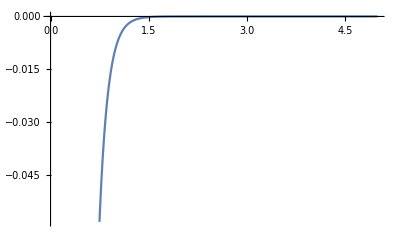

```mathematica
Plot[T[0.5,Cos[π/4],π/3,t],{t, 0,5}]
```

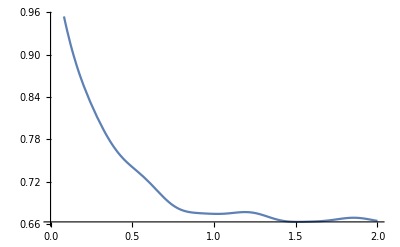

```mathematica
Plot[((ⅇ^(-5!*t)+ⅇ^(-2!*√2*t)+ⅇ^(-3*√3*t))/2.5+SphericalBesselJ[3,10*t]/8+SphericalBesselJ[3,20*t]/20)/2+0.664,{t,0,2}]
```

```mathematica
θ
N[ArcCos[4/(√43)]]
```

θ

0.914743

```mathematica
ϕ
N[2*π/3]
N[π/3]
```

ϕ

2.0944

1.0472

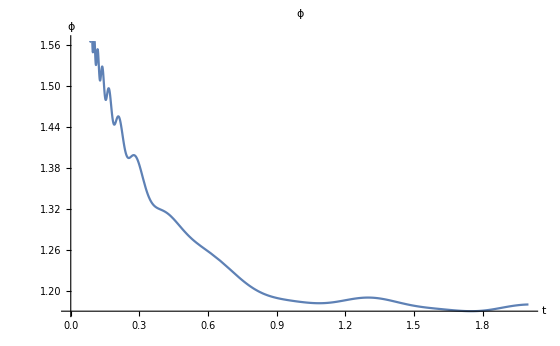

```mathematica
Plot[((ⅇ^(-5!*t)+ⅇ^(-2!*√2*t)+ⅇ^(-3*√3*t))/2.5+SphericalBesselJ[3,9*t]/8+SphericalBesselJ[3,19*t]/20-Sin[5/t]*1/(20*(1+ⅇ^((t+0.6)^6))))/1.4+1.174,{t,0,2},AxesLabel->{HoldForm[t],HoldForm[ϕ]},PlotLabel->HoldForm[ϕ],LabelStyle->{GrayLevel[0]}]
```

Power::infy: Infinite expression 1/0 encountered.

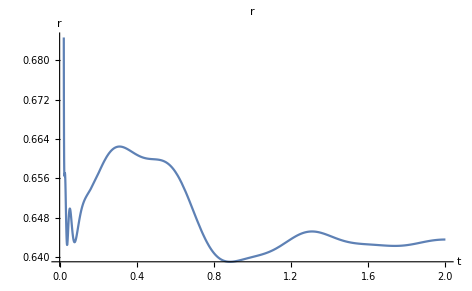

```mathematica
Plot[(SphericalBesselJ[3,9*t]/(8*√t)ⅇ^(-1*t)*1/HeavisideTheta[t-0.02]+SphericalBesselJ[3,19*t]/20*ⅇ^-t-Sin[4/√t]*ⅇ^(-10*t)/(50*(1+ⅇ^((t+0.6)^6)))+1/(10000*(t-0.02)^1))/1.4+0.64295,{t,0,2},AxesLabel->{HoldForm[t],HoldForm[r]},PlotLabel->HoldForm[r],LabelStyle->{GrayLevel[0]}]
```

Power::infy: Infinite expression 1/0 encountered.

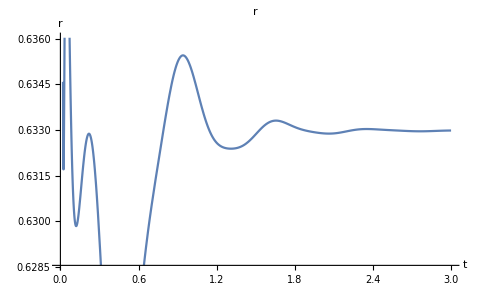

```mathematica
Plot[(-SphericalBesselJ[3,9*t]/6 ⅇ^(-2*t)*1/HeavisideTheta[t-0.02]+SphericalBesselJ[3,19*t]/20*ⅇ^(-2t)-Sin[4/t^(1/3)]*ⅇ^(-2*t)/(50*(1+ⅇ^((t+0.6)^6)))+1/(10000*(t-0.01)^1))/1.4+0.63295,{t,0,3},AxesLabel->{HoldForm[t],HoldForm[r]},PlotLabel->HoldForm[r],LabelStyle->{GrayLevel[0]}]
```

Power::infy: Infinite expression 1/0 encountered.

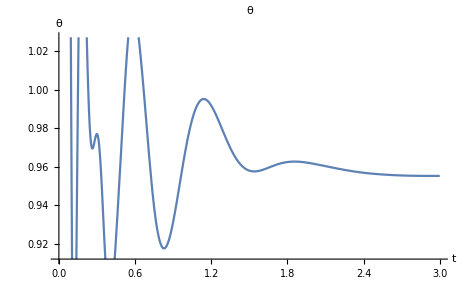

```mathematica
Plot[-(SphericalBesselJ[8,10*t]/-10*ⅇ/HeavisideTheta[t-0.08]-BesselJ[2,50*t] ⅇ^(-2*t)/(1+ⅇ^((t+0.4)^6))*ⅇ^-t-Sin[ⅇ^(-0.5t)]/6+BesselJ[3,-10*Log[t]]*ⅇ^(-(t-0.5))ⅇ^(-2t)/(1+ⅇ^((t+0.5)^2))-BesselJ[1,10*Log[t]]*ⅇ^(-(t-0.5)^4)/1+Sin[10/t^(1/3)]*1/(1+ⅇ^((t+0.6)^2)))*2^(-2t)/(HeavisideTheta[t-0.08] +1.9)+Sin[2^(-10(t-2)^2)]2^(-2t)/10+0.955,{t,0,3},AxesLabel->{HoldForm[t],HoldForm[θ]},PlotLabel->HoldForm[θ],LabelStyle->{GrayLevel[0]}]
```